```mathematica
SetDirectory[NotebookDirectory[]];
```

### Definitions

```mathematica
k0=kp Cosh[ηk];
kx=kp Cos[ϕk];
ky=kp Sin[ϕk];
kz=kp Sinh[ηk];
kplus=FullSimplify[k0-kz];
kminus=FullSimplify[k0+kz];

ϕg=0;
kgx=kg0 Sin[θg]Cos[ϕg];
kgy=kg0 Sin[θg]Sin[ϕg];
kgz=kg0 Cos[θg];
kgplus=FullSimplify[kg0-kgz];
kgminus=FullSimplify[kg0+kgz];

g0=1;
gx=Sin[θg]Cos[ϕg];
gy=Sin[θg]Sin[ϕg];
gz=Cos[θg];
gplus=FullSimplify[g0-gz];
gminus=FullSimplify[g0+gz];
```

```mathematica
k3vec={kx,ky,kz};
kg3vec={kgx,kgy,kgz};
g3vec={gx,gy,gz};
```

### Simplifications

#### Phase space

```mathematica
FullSimplify[kplus-(k0 g0-k3vec.g3vec)]
```

kp Cos[ϕk] Sin[θg]+kp (-1+Cos[θg]) Sinh[ηk]

```mathematica
FullSimplify[-kp^2-kz^2]
```

-kp^2 Cosh[ηk]^2

#### Matrix element

```mathematica
m1=FullSimplify[2/(kplus kminus)]
```

2/kp^2

#### Measurement function

```mathematica
FullSimplify[(k0 g0-k3vec.g3vec)]
```

kp (Cosh[ηk]-Cos[ϕk] Sin[θg]-Cos[θg] Sinh[ηk])

```mathematica
FullSimplify[(kplus-(k0 g0-k3vec.g3vec))/kp]
```

Cos[ϕk] Sin[θg]+(-1+Cos[θg]) Sinh[ηk]

```mathematica
FullSimplify[Sin[x]/(1-Cos[x])]
```

Cot[x/2]

```mathematica
FullSimplify[(-kplus+(k0 g0-k3vec.g3vec))/kp]
```

-Cos[ϕk] Sin[θg]+Sinh[ηk]-Cos[θg] Sinh[ηk]

#### Soft drop groomer

```mathematica
FullSimplify[kplus-k0 gplus]
```

kp (Cos[θg] Cosh[ηk]-Sinh[ηk])

```mathematica
FullSimplify[(k0 g0-k3vec.g3vec)-k0 gplus]
```

kp (ⅇ^-ηk Cos[θg]-Cos[ϕk] Sin[θg])

#### Jacobian

```mathematica
FullSimplify[Det[({{1, 0, 0, 0}, {0, Cos[ϕk], -kp Sin[ϕk], 0}, {0, Sin[ϕk], kp Cos[ϕk], 0}, {0, Sinh[ηk], 0, kp Cosh[ηk]}})]]
```

kp^2 Cosh[ηk]

## Integration

### Near the gluon

```mathematica
FullSimplify[Reduce[{0<θ<Pi/2,Cos[ϕ]Cot[θ/2]>Sinh[η],Cos[θ]>Tanh[η],Cot[θ]>Exp[η]Cos[ϕ]},η,Reals]]
```

Reduce::ztest: Unable to decide whether numeric quantities {-π-8 ArcTan[1-√2],3 π-8 ArcTan[1+√2]} are equal to zero. Assuming they are.

θ>0&&2 θ<π&&(η<Log[Cot[θ] Sec[ϕ]]||2 Cos[ϕ]+Tan[θ/2]^2<1)&&(η+Log[2]<Log[2 √(Cos[ϕ]^2 Csc[θ/2]^2+Sin[ϕ]^2)+Cos[ϕ] (Cot[θ/4]-Tan[θ/4])]||2 Cos[ϕ]+Tan[θ/2]^2≥1)

```mathematica
region=FullSimplify[Reduce[{0<θ<Pi/2,Exp[η]<Cos[ϕ]Cot[θ/2]+√(1+Cos[ϕ]^2Cot[θ/2]^2),Exp[η]<Cot[θ/2],Exp[η]Cos[ϕ]<Cot[θ]},η,Reals]]
```

Reduce::ztest: Unable to decide whether numeric quantities {-π-8 ArcTan[1-√2],3 π-8 ArcTan[1+√2]} are equal to zero. Assuming they are.

θ>0&&2 θ<π&&(η<Log[Cot[θ] Sec[ϕ]]||2 Cos[ϕ]+Tan[θ/2]^2<1)&&(η+Log[2]<Log[2 √(Cos[ϕ]^2 Csc[θ/2]^2+Sin[ϕ]^2)+Cos[ϕ] (Cot[θ/4]-Tan[θ/4])]||2 Cos[ϕ]+Tan[θ/2]^2≥1)

Less::nord: Invalid comparison with -0.549306+3.14159 ⅈ attempted.

Less::nord: Invalid comparison with 1.25496+3.14159 ⅈ attempted.

Less::nord: Invalid comparison with 1.94469+3.14159 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

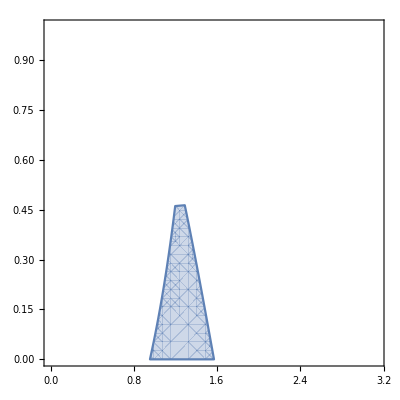

```mathematica
RegionPlot[region/.θ->Pi/3.,{ϕ,0,Pi},{η,0,1}]
```

```mathematica
NIntegrate[Boole[region/.θ->Pi/3],{ϕ,0,Pi},{η,0,Infinity}]
```

0.163563

```mathematica
NIntegrate[-Boole[Cos[ϕ]Cot[θ/2]>Sinh[η]&&Cos[θ]>Tanh[η]&&Cot[θ]>Exp[η]Cos[ϕ]]/.θ->Pi/3.,{ϕ,0,Pi},{η,0,Infinity}]
```

-0.163563

```mathematica
-NIntegrate[(Boole[1>2Cos[ϕ]+Tan[θ/2]^2&&ArcSinh[Cos[ϕ]Cot[θ/2]]>η]+Boole[1<2Cos[ϕ]+Tan[θ/2]^2&&Log[Sec[ϕ]Cot[θ]]>η])/.θ->Pi/3.,{ϕ,0,Pi},{η,0,Infinity}]
```

-0.163563

```mathematica
-NIntegrate[(Boole[1>2Cos[ϕ]+Tan[θ/2]^2&&ArcSinh[Cos[ϕ]Cot[θ/2]]>0]ArcSinh[Cos[ϕ]Cot[θ/2]]+Boole[1<2Cos[ϕ]+Tan[θ/2]^2&&Log[Sec[ϕ]Cot[θ]]>0]Log[Sec[ϕ]Cot[θ]])/.θ->Pi/3.,{ϕ,0,Pi}]
```

-0.163563

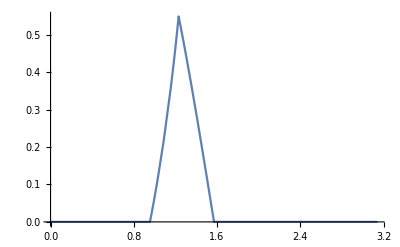

```mathematica
Plot[(HeavisideTheta[1-2Cos[ϕ]-Tan[θ/2]^2]HeavisideTheta[ArcSinh[Cos[ϕ]Cot[θ/2]]]ArcSinh[Cos[ϕ]Cot[θ/2]]+HeavisideTheta[-1+2Cos[ϕ]+Tan[θ/2]^2]HeavisideTheta[Log[Sec[ϕ]Cot[θ]]]Log[Sec[ϕ]Cot[θ]])/.θ->Pi/3.,{ϕ,0,Pi},PlotRange->All]
```

```mathematica
FullSimplify[Reduce[{0<θ<Pi/2,0<ϕ<Pi/2,1>2Cos[ϕ]+Tan[θ/2]^2},ϕ,Reals]]
```

Reduce::ztest: Unable to decide whether numeric quantities {-π-8 ArcTan[1-√2],3 π-8 ArcTan[1+√2]} are equal to zero. Assuming they are.

θ>0&&2 θ<π&&ArcSec[1+Sec[θ]]<ϕ&&2 ϕ<π

```mathematica
NIntegrate[(Boole[1>2Cos[ϕ]+Tan[θ/2]^2&&ArcSinh[Cos[ϕ]Cot[θ/2]]>0]ArcSinh[Cos[ϕ]Cot[θ/2]])/.θ->Pi/3.,{ϕ,0,Pi}]
```

0.0965229

```mathematica
NIntegrate[Boole[ϕ>ArcSec[1+Sec[θ]]]ArcSinh[Cos[ϕ]Cot[θ/2]]/.θ->Pi/3.,{ϕ,0,Pi/2}]
```

0.0965229

```mathematica
Assuming[0<θ<Pi/2,Integrate[ArcSinh[Cos[ϕ]Cot[θ/2]],{ϕ,ArcSec[1+Sec[θ]],Pi/2}]]
```

∫_ArcSec[1+Sec[θ]]^(π/2) ArcSinh[Cos[ϕ] Cot[θ/2]]ⅆϕ

```mathematica
NIntegrate[Boole[Cos[ϕ]Cot[θ/2]>Sinh[η]]/.θ->Pi/3.,{ϕ,0,Pi},{η,0,Infinity}]
```

1.42102

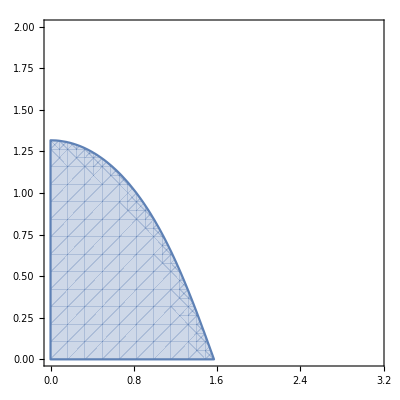

```mathematica
RegionPlot[Cos[ϕ]Cot[θ/2]>Sinh[η]/.θ->Pi/3,{ϕ,0,Pi},{η,0,2}]
```

```mathematica
NIntegrate[HeavisideTheta[ArcSinh[Cos[ϕ]Cot[θ/2]]]ArcSinh[Cos[ϕ]Cot[θ/2]]/.θ->Pi/3,{ϕ,0,Pi}]
```

1.42102

```mathematica
Integrate[ArcSinh[Cos[ϕ]Cot[θ/2.]]/.θ->Pi/3,{ϕ,0,Pi/2.}]
```

∫_0^1.5708 ArcSinh[1.73205 Cos[ϕ]]ⅆϕ

```mathematica
TrigToExp[ArcSinh[a Cos[x]]]
```

Log[1/2 a (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))+√(1+1/4 a^2 (ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))^2)]

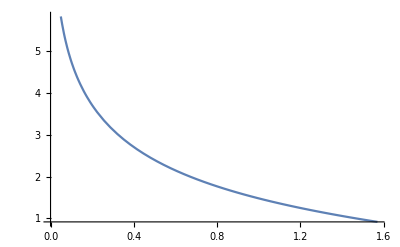

```mathematica
Plot[NIntegrate[ArcSinh[Cos[ϕ]Cot[θ/2]],{ϕ,0,Pi/2}],{θ,0,Pi/2}]
```

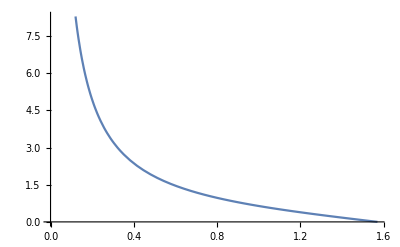

```mathematica
Plot[Cot[x],{x,0,Pi/2}]
```

```mathematica
Reduce[{0<ϕ<Pi,0<θ<Pi/2,Sec[ϕ]>Tan[θ]},ϕ,Reals]
```

Reduce::ztest1: Unable to decide whether numeric quantity -π-8 ArcTan[1-√2] is equal to zero. Assuming it is.

(0<θ<-2 ArcTan[1-√2]&&0<ϕ<π/2)||(θ==-2 ArcTan[1-√2]&&0<ϕ<π/2)||(-2 ArcTan[1-√2]<θ<π/2&&ArcCos[1/2 Cot[θ/2] (1-Tan[θ/2]^2)]<ϕ<π/2)

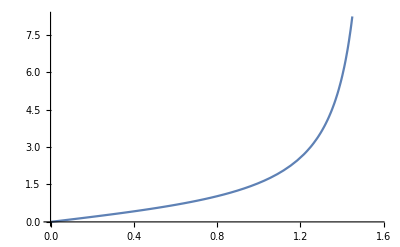

```mathematica
Plot[Tan[θ],{θ,0,Pi/2}]
```

```mathematica
Tan[Pi/4]
```

1

```mathematica
intval=Integrate[Log[Sec[x]a],x]
```

-(ⅈ x^2)/2+x Log[1+ⅇ^(2 ⅈ x)]+x Log[a Sec[x]]-1/2 ⅈ PolyLog[2,-ⅇ^(2 ⅈ x)]

```mathematica
FullSimplify[(1+ⅇ^(2 ⅈ x))(a Sec[x])]
```

2 a ⅇ^(ⅈ x)

```mathematica
PolyLog[2,-1]
```

-π^2/12

```mathematica
numericsGluon=Table[{θ,
NIntegrate[Boole[Cos[ϕ]Cot[θ/2]>Sinh[η]],{ϕ,0.,Pi},{η,0.,Infinity}]-NIntegrate[Boole[Cos[ϕ]Cot[θ/2]>Sinh[η]](Boole[Cos[θ]>Tanh[η]&&Cot[θ]>Exp[η]Cos[ϕ]]),{ϕ,0.,Pi},{η,0.,Infinity}]},
{θ,0.01,Pi/2.,Pi/40.}]
```

{{0.01,1.01498},{0.0885398,1.01785},{0.16708,1.02536},{0.245619,1.03767},{0.324159,1.05508},{0.402699,1.078},{0.481239,1.107},{0.559779,1.14285},{0.638319,1.18658},{0.716858,1.23957},{0.795398,1.301},{0.873938,1.31179},{0.952478,1.29509},{1.03102,1.26484},{1.10956,1.22621},{1.1881,1.18186},{1.26664,1.13327},{1.34518,1.0813},{1.42372,1.02637},{1.50226,0.968659}}

```mathematica
analyticGluon[θ_]:=NIntegrate[ArcSinh[Cos[ϕ]Cot[θ/2]],{ϕ,0,ArcSec[1+Sec[θ]]}]-I/2 ArcSec[1+Sec[θ]]^2-ArcSec[1+Sec[θ]]Log[2Cot[θ]]+I/2 PolyLog[2,-Exp[2I ArcSec[1+Sec[θ]]]]+HeavisideTheta[Pi/4-θ](I Pi^2)/24+HeavisideTheta[θ-Pi/4](I/2 ArcSec[Tan[θ]]^2+ArcSec[Tan[θ]]Log[2Cot[θ]]-I/2 PolyLog[2,-Exp[2I ArcSec[Tan[θ]]]])
```

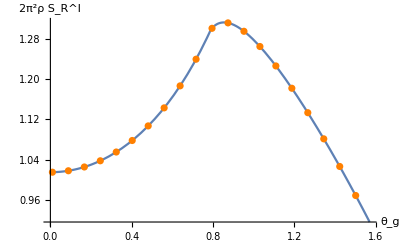

```mathematica
plotGluon1=Plot[analyticGluon[θ],{θ,0,Pi/2}];plotGluon2=ListPlot[numericsGluon,PlotStyle->Orange];plotGluon=Show[plotGluon1,plotGluon2,AxesLabel->{"θ_g","2π^2ρ S_R^I"}]
```

```mathematica
Export["figures/gluon_numerics.pdf",plotGluon,"PDF"]
```

figures/gluon_numerics.pdf

### Near the quark

```mathematica
Series[(1/(Cosh[η]-Cos[ϕ]Sin[θ]-Sinh[η]Cos[θ]))^(-2ϵ)Sin[ϕ]^(-2ϵ),{ϵ,0,1}]
```

1-2 (Log[Sin[ϕ]]+Log[1/(Cosh[η]-Cos[ϕ] Sin[θ]-Cos[θ] Sinh[η])]) ϵ+O[ϵ]^2

```mathematica
intval=Assuming[{0<θ<Pi/2},FullSimplify[Integrate[(1/(Cosh[η]-Cos[ϕ]Sin[θ]-Sinh[η]Cos[θ]))^(-2ϵ),η]]]
```

-1/(1+2 ϵ)ⅈ AppellF1[1+2 ϵ,1/2,1/2,2 (1+ϵ),(Cos[ϕ]-Cosh[η] Csc[θ]+Cot[θ] Sinh[η])/(-1+Cos[ϕ]),(Cos[ϕ]-Cosh[η] Csc[θ]+Cot[θ] Sinh[η])/(1+Cos[ϕ])] Sech[η-ArcTanh[Sec[θ]]] (1/(Cosh[η]-Cos[ϕ] Sin[θ]-Cos[θ] Sinh[η]))^(-2 ϵ) √((1+Cosh[η] Csc[θ]-Cot[θ] Sinh[η])/(1+Cos[ϕ])) (Cos[ϕ]-Cosh[η] Csc[θ]+Cot[θ] Sinh[η]) √((-1-ⅈ Sinh[η-ArcTanh[Sec[θ]]])/(-1+Cos[ϕ]))

```mathematica
FullSimplify[((1+Cosh[η] Csc[θ]-Cot[θ] Sinh[η])/(1+Cos[ϕ]))((-1-ⅈ Sinh[η-ArcTanh[Sec[θ]]])/(-1+Cos[ϕ]))]
```

Csc[ϕ]^2 (1+Cosh[η] Csc[θ]-Cot[θ] Sinh[η]) (1+ⅈ Sinh[η-ArcTanh[Sec[θ]]])

```mathematica
Assuming[0<θ<Pi/2,FullSimplify[TrigToExp[Expand[(1+Cosh[η] Csc[θ]-Cot[θ] Sinh[η]) (1+ⅈ Sinh[η-ArcTanh[Sec[θ]]])]]]]
```

-ⅇ^-η Csc[θ] (Cos[θ/2]+ⅇ^η Sin[θ/2])^2 (-1+Cosh[η] Csc[θ]-Cot[θ] Sinh[η])